```mathematica
phi11=ω;
phi12=ⅈ k;
phi21=(-105+35ⅈ We δ^3 k^3-84 δ^2 k^2 -ⅈ δ k(18 Rey -35 Cot[θ]-210 m))/(14δ Rey);
phi22=(35+63 δ^2 k^2-δ  m(210ⅈ k+35ω)+δ Rey(34ⅈ k+14ω))/(14δ Rey);
```

```mathematica
M=({{phi11, phi12}, {phi21, phi22}});
```

```mathematica
stabBound=Det[M]==0//Simplify
```

(-84 ⅈ k^3 δ^2-35 k^4 We δ^3-3 k^2 δ (70 m-6 Rey+21 δ ω)+ⅈ k (-105+210 m δ ω-34 Rey δ ω)+7 ω (-5+5 m δ ω-2 Rey δ ω)-35 k^2 δ Cot[θ])/(Rey δ)==0

```mathematica
stabBoundSub1=-84 ⅈ k^3 δ^2-35 k^4 We δ^3-3 k^2 δ (70 m-6 Rey+21 δ ω)+ⅈ k (-105+210 m δ ω-34 Rey δ ω)+7 ω (-5+5 m δ ω-2 Rey δ ω)-35 k^2 δ Cot[θ]==0/.{ω->(ωr+ⅈ ωi)}//Simplify
```

-84 ⅈ k^3 δ^2+ⅈ k (-105+210 m δ (ⅈ ωi+ωr)-34 Rey δ (ⅈ ωi+ωr))+7 (ⅈ ωi+ωr) (-5+5 m δ (ⅈ ωi+ωr)-2 Rey δ (ⅈ ωi+ωr))==k^2 δ (210 m-18 Rey+35 k^2 We δ^2+63 ⅈ δ ωi+63 δ ωr+35 Cot[θ])

```mathematica
stabBoundSub1Im=ComplexExpand[Im[stabBoundSub1]]//Simplify
```

84 k^3 δ^2+63 k^2 δ^2 ωi+7 ωi (5-10 m δ ωr+4 Rey δ ωr)+k (105-210 m δ ωr+34 Rey δ ωr)==0

```mathematica
stabBoundSub1Re=ComplexExpand[Re[stabBoundSub1]]//Simplify
```

k (-210 m δ ωi+34 Rey δ ωi)==7 (5 ωr+5 m δ (ωi^2-ωr^2)+2 Rey δ (-ωi^2+ωr^2))+k^2 δ (210 m-18 Rey+35 k^2 We δ^2+63 δ ωr+35 Cot[θ])

```mathematica
Solve[{stabBoundSub1Im,stabBoundSub1Re},{ωi,ωr}]
```

```mathematica
Solve[stabBoundSub1Im,ωi]//Simplify
```

{{ωi→-(k (105+84 k^2 δ^2-210 m δ ωr+34 Rey δ ωr))/(7 (5+9 k^2 δ^2-10 m δ ωr+4 Rey δ ωr))}}

```mathematica
stabBoundSub1Re2=stabBoundSub1Re/.{ωi->-(k (105+84 k^2 δ^2-210 m δ ωr+34 Rey δ ωr))/(7 (5+9 k^2 δ^2-10 m δ ωr+4 Rey δ ωr))}//Simplify
```

(2 k^2 (105 m-17 Rey) δ (105+84 k^2 δ^2-210 m δ ωr+34 Rey δ ωr))/(7 (5+9 k^2 δ^2-10 m δ ωr+4 Rey δ ωr))==7 (5 ωr+2 Rey δ (ωr^2-(k^2 (105+84 k^2 δ^2-210 m δ ωr+34 Rey δ ωr)^2)/(49 (5+9 k^2 δ^2-10 m δ ωr+4 Rey δ ωr)^2))+5 m δ (-ωr^2+(k^2 (105+84 k^2 δ^2-210 m δ ωr+34 Rey δ ωr)^2)/(49 (5+9 k^2 δ^2-10 m δ ωr+4 Rey δ ωr)^2)))+k^2 δ (210 m-18 Rey+35 k^2 We δ^2+63 δ ωr+35 Cot[θ])

```mathematica
Assuming[{_∈PositiveReals},FullSimplify[stabBoundSub1Re2]]
```

(k^2 (3675 m^2+37 Rey^2) δ)/(7 (5 m-2 Rey))+7 (5 m-2 Rey) δ ωr^2==35 k^4 We δ^3+7 (5+9 k^2 δ^2) ωr+(25 δ (25 k Rey+3 k^3 (35 m+Rey) δ^2)^2)/(7 (5 m-2 Rey) (5+δ (9 k^2 δ-10 m ωr+4 Rey ωr))^2)+35 k^2 δ Cot[θ]

```mathematica
stabBoundSub1Re2Simp=(k^2 (3675 m^2+37 Rey^2) δ)/(7 (5 m-2 Rey))+7 (5 m-2 Rey) δ ωr^2==35 k^4 We δ^3+7 (5+9 k^2 δ^2) ωr+(25 δ (25 k Rey+3 k^3 (35 m+Rey) δ^2)^2)/(7 (5 m-2 Rey) (5+δ (9 k^2 δ-10 m ωr+4 Rey ωr))^2)+35 k^2 δ Cot[θ];
```

```mathematica
Solve[stabBoundSub1Re2Simp,ωr]
```

{{ωr→1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2-√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]-√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))))},{ωr→1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2+√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]-√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))))},{ωr→1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2-√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]+√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))))},{ωr→1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2+√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]+√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))))}}

```mathematica
wrSol1=1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2-√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]-√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))));
wrSol2=1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2+√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]-√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))));
wrSol3=1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2-√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]+√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))));
wrSol4=1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2+√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]+√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))));
```

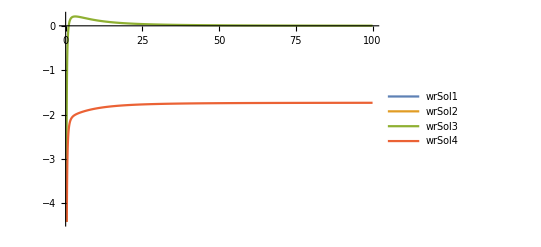

```mathematica
Plot[{wrSol1/.{θ->(4.0 Degree),m->0.15, Rey->((3.0*0.7^2)/Tan[4.0 Degree]),δ->Tan[4.0 Degree],We->0,k->(2π)/λ},wrSol2/.{θ->(4.0 Degree),m->0.15, Rey->((3.0*0.7^2)/Tan[4.0 Degree]),δ->Tan[4.0 Degree],We->0,k->(2π)/λ},wrSol3/.{θ->(4.0 Degree),m->0.15, Rey->((3.0*0.7^2)/Tan[4.0 Degree]),δ->Tan[4.0 Degree],We->0,k->(2π)/λ}, wrSol4/.{θ->(4.0 Degree),m->0.15, Rey->((3.0*0.7^2)/Tan[4.0 Degree]),δ->Tan[4.0 Degree],We->0,k->(2π)/λ}},{λ,0,100}, PlotLegends-> {"wrSol1", "wrSol2", "wrSol3","wrSol4"}]
```

```mathematica
wrSol1/.{θ->(4.0 Degree),m->0.15, Rey->((3.0*0.7^2)/Tan[4.0 Degree]),δ->Tan[4.0 Degree],We->0}
```

-0.173157 (5+0.0440078 k^2-√((-5-0.0440078 k^2)^2+0.0102041 (-1225.-3172.8 k^2-0.0948978 k^4-√((1225.+3172.8 k^2+0.0948978 k^4)^2+2263.84 (0.+4872.24 k^2-102.917 k^4-0.522097 k^6)))))

```mathematica
wrSolFinalBound=Assuming[{_∈PositiveReals},FullSimplify[1/(2 (5 m δ-2 Rey δ))(5+9 k^2 δ^2-√((-5-9 k^2 δ^2)^2+1/(980 m δ-392 Rey δ)2 (5 m δ-2 Rey δ) (-1225-4410 k^2 δ^2-14700 k^2 m^2 δ^2-148 k^2 Rey^2 δ^2-3969 k^4 δ^4+4900 k^4 m We δ^4-1960 k^4 Rey We δ^4+4900 k^2 m δ^2 Cot[θ]-1960 k^2 Rey δ^2 Cot[θ]+√((1225+4410 k^2 δ^2+14700 k^2 m^2 δ^2+148 k^2 Rey^2 δ^2+3969 k^4 δ^4-4900 k^4 m We δ^4+1960 k^4 Rey We δ^4-4900 k^2 m δ^2 Cot[θ]+1960 k^2 Rey δ^2 Cot[θ])^2-4 (980 m δ-392 Rey δ) (18375 k^2 m δ+7350 k^2 Rey δ+66150 k^4 m δ^3+210 k^4 Rey δ^3-6125 k^4 We δ^3+4410 k^6 m δ^5-1386 k^6 Rey δ^5-22050 k^6 We δ^5-19845 k^8 We δ^7-6125 k^2 δ Cot[θ]-22050 k^4 δ^3 Cot[θ]-19845 k^6 δ^5 Cot[θ])))))==0]]
```

1/((5 m-2 Rey) δ)(70+126 k^2 δ^2-√(2450+98 k^4 (81+100 m We-40 Rey We) δ^4-4 k^2 δ^2 (-2205+7350 m^2+74 Rey^2+490 (-5 m+2 Rey) Cot[θ])+2 √((1225+2 k^2 (2205+7350 m^2+74 Rey^2) δ^2+49 k^4 (81-100 m We+40 Rey We) δ^4-980 k^2 (5 m-2 Rey) δ^2 Cot[θ])^2+5488 k^2 (5 m-2 Rey) δ^2 (-525 (5 m+2 Rey)-5 k^2 (1890 m+6 Rey-175 We) δ^2+18 k^4 (-35 m+11 Rey+175 We) δ^4+2835 k^6 We δ^6+35 (5+9 k^2 δ^2)^2 Cot[θ]))))==0

```mathematica
wrSolFinalBound2=70+126 k^2 δ^2-√(2450+98 k^4 (81+100 m We-40 Rey We) δ^4-4 k^2 δ^2 (-2205+7350 m^2+74 Rey^2+490 (-5 m+2 Rey) Cot[θ])+2 √((1225+2 k^2 (2205+7350 m^2+74 Rey^2) δ^2+49 k^4 (81-100 m We+40 Rey We) δ^4-980 k^2 (5 m-2 Rey) δ^2 Cot[θ])^2+5488 k^2 (5 m-2 Rey) δ^2 (-525 (5 m+2 Rey)-5 k^2 (1890 m+6 Rey-175 We) δ^2+18 k^4 (-35 m+11 Rey+175 We) δ^4+2835 k^6 We δ^6+35 (5+9 k^2 δ^2)^2 Cot[θ])))==0
```

70+126 k^2 δ^2-√(2450+98 k^4 (81+100 m We-40 Rey We) δ^4-4 k^2 δ^2 (-2205+7350 m^2+74 Rey^2+490 (-5 m+2 Rey) Cot[θ])+2 √((1225+2 k^2 (2205+7350 m^2+74 Rey^2) δ^2+49 k^4 (81-100 m We+40 Rey We) δ^4-980 k^2 (5 m-2 Rey) δ^2 Cot[θ])^2+5488 k^2 (5 m-2 Rey) δ^2 (-525 (5 m+2 Rey)-5 k^2 (1890 m+6 Rey-175 We) δ^2+18 k^4 (-35 m+11 Rey+175 We) δ^4+2835 k^6 We δ^6+35 (5+9 k^2 δ^2)^2 Cot[θ])))==0

```mathematica
Solve[wrSolFinalBound2,Rey]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Rey→(5 m)/2},{Rey→-(35 (k^2 We δ^2 (5+9 k^2 δ^2)^2-3 m (25+90 k^2 δ^2+6 k^4 δ^4)+(5+9 k^2 δ^2)^2 Cot[θ]))/(6 (-175-5 k^2 δ^2+33 k^4 δ^4))}}

```mathematica
ReyCrit=-(35 (k^2 We δ^2 (5+9 k^2 δ^2)^2-3 m (25+90 k^2 δ^2+6 k^4 δ^4)+(5+9 k^2 δ^2)^2 Cot[θ]))/(6 (-175-5 k^2 δ^2+33 k^4 δ^4));
```

```mathematica
Limit[ReyCrit,k->0]
```

1/30 (-75 m+25 Cot[θ])

```mathematica
FrCritEqn=((3 Fr^2)/δ)==-(35 (k^2 We δ^2 (5+9 k^2 δ^2)^2-3 m (25+90 k^2 δ^2+6 k^4 δ^4)+(5+9 k^2 δ^2)^2 (1/δ)))/(6 (-175-5 k^2 δ^2+33 k^4 δ^4))//Simplify
```

(18 Fr^2+(35 ((5+9 k^2 δ^2)^2 (1+k^2 We δ^3)-3 m δ (25+90 k^2 δ^2+6 k^4 δ^4)))/(-175-5 k^2 δ^2+33 k^4 δ^4))/δ==0

```mathematica
Solve[FrCritEqn,Fr]//Simplify
```

{{Fr→-(√(-(5+9 k^2 δ^2)^2 (1+k^2 We δ^3)+3 m δ (25+90 k^2 δ^2+6 k^4 δ^4)))/(3 √(-10-(2 k^2 δ^2)/7+(66 k^4 δ^4)/35))},{Fr→(√(-(5+9 k^2 δ^2)^2 (1+k^2 We δ^3)+3 m δ (25+90 k^2 δ^2+6 k^4 δ^4)))/(3 √(-10-(2 k^2 δ^2)/7+(66 k^4 δ^4)/35))}}

```mathematica
FrSol=(√(-(5+9 k^2 δ^2)^2 (1+k^2 We δ^3)+3 m δ (25+90 k^2 δ^2+6 k^4 δ^4)))/(3 √(-10-(2 k^2 δ^2)/7+(66 k^4 δ^4)/35));
```

```mathematica
FrSolLambda=FrSol/.{k->((2π)/λ)}
```

(√(3 m δ (25+(96 π^4 δ^4)/λ^4+(360 π^2 δ^2)/λ^2)-(5+(36 π^2 δ^2)/λ^2)^2 (1+(4 π^2 We δ^3)/λ^2)))/(3 √(-10+(1056 π^4 δ^4)/(35 λ^4)-(8 π^2 δ^2)/(7 λ^2)))

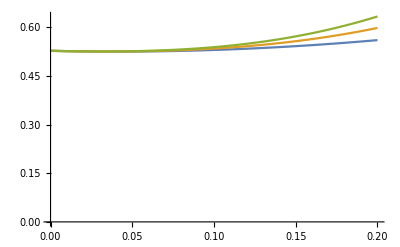

```mathematica
Plot[{FrSolLambda/.{m->0.15, λ->5,We->0},FrSolLambda/.{m->0.15, λ->5,We->10},FrSolLambda/.{m->0.15, λ->5,We->20} },{δ,0.0001,0.2},PlotRange->{0,Automatic}]
```

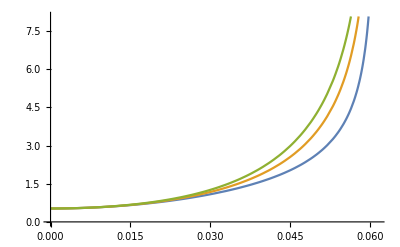

```mathematica
Plot[{FrSolLambda/.{m->0.15, λ->0.25,We->0},FrSolLambda/.{m->0.15, λ->0.25,We->10},FrSolLambda/.{m->0.15, λ->0.25,We->20} },{δ,0.0001,0.2},PlotRange->{0,Automatic}]
```

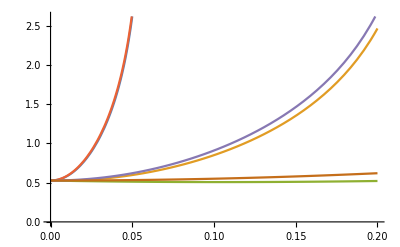

```mathematica
Plot[{FrSolLambda/.{m->0.5, λ->0.25,We->0},FrSolLambda/.{m->0.5, λ->1,We->0},FrSolLambda/.{m->0.5, λ->4,We->0}, FrSolLambda/.{m->0.0, λ->0.25,We->0},FrSolLambda/.{m->0.0, λ->1,We->0},FrSolLambda/.{m->0.0, λ->4,We->0}},{δ,0.0001,0.2},PlotRange->{0,Automatic}]
```

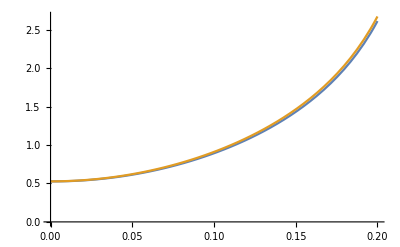

```mathematica
Plot[{FrSolLambda/.{m->0.15, λ->1,We->0},FrSolLambda/.{m->0.0, λ->1,We->0}},{δ,0.0001,0.2},PlotRange->{0,Automatic}]
```